# CCD Defect Mitigation Development

```mathematica
(* Start with filesToProcess and metaDataByRawFilename setup from Juno28i360 *)
```

### References

```mathematica
(*
 https://en.wikipedia.org/wiki/Flat-field_correction
http://star-www.rl.ac.uk/docs/sc5.htx/sc5se5.html
 *)
```

## Generate Debias and Gain

```mathematica
(*
In Juno3D
evaluate "Setup, Prompt, Load Metadata"
select "PJ00-18-tdi-1.txt"
Here, evaluate this "Generate Debias and Gain" section
debias and gain images located at bottom are cut and pasted into Juno28
*)
```

```mathematica
filesToProcess//Length (* 368 *)
```

263

```mathematica
Sort[Keys[metaDataByRawFilename⟦1⟧]]
```

{COMPRESSION_TYPE,DATA_SET_ID,DESCRIPTION,EXPOSURE_DURATION,FILE_NAME,FILE_RECORDS,FILTER_NAME,FOCAL_PLANE_TEMPERATURE,IMAGE_TIME,INSTRUMENT_HOST_NAME,INSTRUMENT_ID,INSTRUMENT_NAME,INTERFRAME_DELAY,JNO:TDI_STAGES_COUNT,LINE_PREFIX_BYTES,LINES,LINE_SAMPLES,LINE_SUFFIX_BYTES,metaDataFileName,MISSION_PHASE_NAME,ORBIT_NUMBER,PJ,PROCESSING_LEVEL_ID,PRODUCER_ID,PRODUCT_CREATION_TIME,PRODUCT_ID,PRODUCT_VERSION_ID,RATIONALE_DESC,rawFileName,RECORD_BYTES,SAMPLE_BIT_MASK,SAMPLE_BIT_MODE_ID,SAMPLE_BITS,SAMPLE_TYPE,SAMPLING_FACTOR,SEQUENCE_ID,SOFTWARE_NAME,SOLAR_DISTANCE,SOURCE_PRODUCT_ID,SPACECRAFT_ALTITUDE,SPACECRAFT_CLOCK_START_COUNT,SPACECRAFT_CLOCK_STOP_COUNT,SPACECRAFT_NAME,STANDARD_DATA_PRODUCT_ID,START_TIME,STOP_TIME,SUB_SPACECRAFT_LATITUDE,SUB_SPACECRAFT_LONGITUDE,TARGET_NAME,TITLE,TOKEN_ID}

```mathematica
Tally[Values[metaDataByRawFilename⟦filesToProcess,"JNO:TDI_STAGES_COUNT"⟧]] (* number of files at different TDIs, 324 at TDI 1, only a few at other TDIs, so not enough to produce separate "debias" and "flatFields" specific to other TDIs *)
```

{{1,263}}

```mathematica
{{1,324},{3,32},{6,8},{60,4},{16,2},{10,2},{64,74}}(* with M *)
```

{{1,324},{3,32},{6,8},{60,4},{16,2},{10,2},{64,74}}

```mathematica
filesSelected=Select[metaDataByRawFilename,#⟦"JNO:TDI_STAGES_COUNT"⟧==1&]//Keys ; (* TDI 1 images *)
```

```mathematica
filesSelected//Length  (* 324 *)
```

263

```mathematica
filesSelectedDark=Select[metaDataByRawFilename
,#⟦"JNO:TDI_STAGES_COUNT"⟧==1 && #⟦"LINES"⟧/(3*128)>39&
]//Keys ; (* TDI 1 images with >39 frames , to hopefully get truly dark frames, since there is light leakage when junocam pointing in hemisphere containing jupiter *)
```

```mathematica
filesSelectedDark//Length
```

108

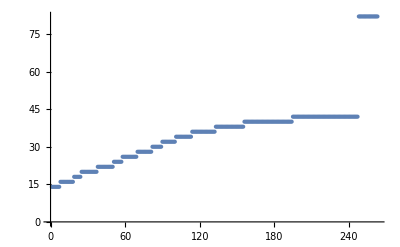

```mathematica
(* numbers of frames distribution *)
ListPlot[Sort[Map[#⟦"LINES"⟧/(3*128)&,Select[metaDataByRawFilename,#⟦"JNO:TDI_STAGES_COUNT"⟧==1&]]]//Values]
```

```mathematica
(* single sample file for tests and information extraction *)
fileName=SelectFirst[filesToProcess,StringContainsQ["14C00024"]]
```

/Users/bswift/Downloads/junoDirs/PJ14/JNCE_2018197_14C00024_V01-raw.png

```mathematica
segmentCorrectionMethod=Identity  (* Disables correction *)
```

Identity

```mathematica
imageObj=loadChannelsFn[fileName];
```

```mathematica
imageObj//Keys
```

{fnPathName,fnBaseName,parsedOK,fnDate,fnOrbit,fnFilter,fnIndex,fnVersion,fnRest,filters,fnType,pds,gzip,dnImage,importedImage,segments}

```mathematica
framelet=imageObj⟦"segments","R"⟧⟦13,1⟧ (* sample uncorrected famelet *)
```

-Graphics-

```mathematica
pixelsInFramelet=Times@@ImageDimensions[framelet]
```

210944

```mathematica
(* Sum of largest n values of image. Approximate with ImageLevels[img,1/dnStep] because bin boundaries are at image values.
Intent is to be fast alternative to TrimmedMean using ImageLevels for Counting Sort
Fails with n==1 *)
topSum[img_Image,nth_Integer]:=Block[
{
il
,ilf
,ilac
,sum
,tf,lw
}
,
il=ImageLevels[img,1/dnStep+1];  
ilf=Map[Reverse[Select[#,#⟦2⟧>0&]]&,il,{-3}];  (* select non-zero bins, and reverse so brighest first. Works with Grayscale and RGB because operating at {-3} level *)
ilac=Transpose[(tf=Transpose[ilf];{tf⟦1⟧,tf⟦2⟧,Accumulate[tf⟦2⟧]})]; (* bin value, number in bin, accumulation of numbers in bin *)
sum=Total[Flatten[{
Map[#⟦1⟧#⟦2⟧&,Take[ilac,lw=LengthWhile[ilac,#⟦3⟧<nth&]]] (* products of values in bins with accumulated count < nth *)
,ilac⟦lw+1,1⟧(nth-ilac⟦Max[lw,1],3⟧) (* product of bin value of bin containing nth value remaining n not from full bins above.
Max[] hack, problem when lw==0 when n vlaues all in first bin(?), need correct fix. *) 
}]];
sum
]
```

### Cont

```mathematica
Round[{.1,.01}pixelsInFramelet]
```

{21094,2109}

```mathematica
(* 
Old Dark framlet metric.
Mean of brightest 10% and 1% of pixels in framelet
*)
imageDarkPixels[framelet_Image]:=Block[
{},Table[topSum[framelet,trim]/trim,{trim,Round[{.1,.01}pixelsInFramelet]}]
]  (* fast compared to using TrimmedMean *)
```

```mathematica
imageDarkPixels[framelet] (* {0.3773336348935454,0.3890737777250935} *)
```

{0.377334,0.389074}

```mathematica
imageInfo[framelet]
```

<|Channels→1,ColorSpace→Automatic,DataRange→{0.,1.},DataType→Real32,Dimensions→{128,1648},SampleDepth→32,Transparency→False,Min→0.,Max→0.399792,Mean→0.307569,Median→0.321987,StandardDeviation→0.0636878|>

```mathematica
(* used as part of full (non-limb) and bright framelet metric *)
(* should be -17 *)
imageEdges[framelet_Image]:=Block[
{topEdge
,bottomEdge
,leftEdge
,rightEdge},
topEdge=Min[Flatten[ImageData[ImageTake[framelet,{1,1},{24,-18}]]]] ;
bottomEdge=Min[Flatten[ImageData[ImageTake[framelet,{-1,-1},{24,-18}]]]] ;
leftEdge=Min[Flatten[ImageData[ImageTake[framelet,{1,-1},{24,24}]]]];
rightEdge=Min[Flatten[ImageData[ImageTake[framelet,{1,-1},{-18,-18}]]]];
{topEdge,bottomEdge,leftEdge,rightEdge}
]
```

```mathematica
Length[filesSelected]
```

263

```mathematica
(* initial stats *)
(* Extract all image edges. Produces per-file list of per-filter associations of per-framelet lists of minimal edge values. Used to determine thresholds for selecting framlets included in flat field *)
AbsoluteTiming[
Parallelize[
allEdges=Map[
(fn=#;
MapIndexed[
<|"edges"-> imageEdges[#]
,"dark"-> imageDarkPixels[#]
,"entropyish"->ByteCount[Compress[#]]
,"energyish"->ImageMeasurements[#,"Total"]
,"entropy"->ImageMeasurements[#,"Entropy"]
,"energy"->ImageMeasurements[#,"Energy"]
,"mean"-> ImageMeasurements[#,"Mean"]
,"median"-> ImageMeasurements[#,"Median"]
,"standardDeviation"-> ImageMeasurements[#,"StandardDeviation"]
,"fileName"-> fn
,"position"-> #2
|>&
,loadChannelsFn[#]⟦"segments"⟧,{3}])&
,filesSelected(*filesSelectedDark*)⟦1;;-1⟧]
];]  (* 126 sec PJ11..14 *)
(* {451.839986,Null} *)
(* 759 sec *)
```

{759.362,Null}

```mathematica
ByteCount[allEdges]
```

60772384

```mathematica
Export["/Users/bswift/Downloads/junoDirs/allEdgesPJ00-18tdi1.mx",allEdges]
```

/Users/bswift/Downloads/junoDirs/allEdgesPJ00-18tdi1.mx

```mathematica
allEdges//Dimensions
```

{263}

## Add SPICE Info

```mathematica
(* compute angle between boreshight and planet center.
Based on code in Juno3D pix2Target3[] and junocamTo3D[].
Angle not actulaly used as selection criterion.  *)
segInfo[segStat_]:=Block[{
fileName
,metaData
,startTimeClockStr
,startTime2
,starTimeShift
,adjustedStartTime
,interframeDelay
,adjustedInterframeDelay
,frameNumber
,gcFrameTime
,target
,targetFrame
,scToTargetMat
,pixVecSC
,pixXY
,pixVecTargetDir
,scPosition
,jupAngle

},
fileName=segStat⟦"fileName"⟧;
metaData=metaDataByRawFilename⟦fileName⟧;
startTimeClockStr=metaData⟦"SPACECRAFT_CLOCK_START_COUNT"⟧;
startTime2=scs2e[junoNacid,startTimeClockStr];
starTimeShift=0.;
adjustedStartTime=startTime2+selectedCameraParams⟦"startTimeBias"⟧;
interframeDelay=ToExpression[First[StringSplit[metaData⟦"INTERFRAME_DELAY"⟧]]];
adjustedInterframeDelay=interframeDelay+selectedCameraParams⟦"ifdAdjustment"⟧;

frameNumber=segStat⟦"position",2⟧;
gcFrameTime=frameTimeForFrameNumber[frameNumber];

If[ToExpression[metaData⟦"ORBIT_NUMBER"⟧]>15, (* skip earlier until have enough spice *)
target="JUPITER";
targetFrame="IAU_"<>target;
scToTargetMat=sxform["JUNO_SPACECRAFT",targetFrame,gcFrameTime];
pixXY=ccdSize/2; (* boresight *)

pixVecSC=(xfCCDtoSC.forwardTransformOpt9v[
normalizeXY[pixXY]
,selectedCameraParams]); (* pixels imaging direction in SC frame *)
pixVecTargetDir=(scToTargetMat.Join[pixVecSC,{0.,0.,0.}])⟦1;;3⟧;

scPosition=(spkezra["JUNO_SPACECRAFT",gcFrameTime,"IAU_"<>target,"NONE"(*"CN+S"*),target])⟦1;;3⟧;
jupAngle=VectorAngle[pixVecTargetDir,{0,0,0}-scPosition]; (* VectorAngle between vector from sc in pixVec direction and vector from sc to jup center *)
,jupAngle=0.;
];

<|"frameTime"-> gcFrameTime
,"frameTimeUTC"->et2utc[gcFrameTime,"ISOC",4]
,"jupAngleDeg"-> jupAngle /Degree
|>
]
```

```mathematica
segStats=Map[
Join[#
,parseJunocamFilename[#⟦"fileName"⟧]
,segInfo[#]
,<|"darkMetric"-> #⟦"entropyish"⟧/#⟦"energyish"⟧|> (* ByteCount[Compress[img]]/ImageMeasurements[img,"Total"] *)
]&
,Flatten@Values[allEdges]]; (* add parsed filename bits and SPICE derrived info to stats *)
```

```mathematica
ByteCount[segStats] (* 121811888 before SPICE *)
```

137535888

```mathematica
segStats//Dimensions
```

{28302}

## Dark Segments (From SegsAnalysisDev.nb)

```mathematica
(* selecting 300 darkest segments from PJ18 *)
tdark=Flatten[Table[
SortBy[Select[segStats, #⟦"fnOrbit"⟧ == "18"&&#⟦"position",1⟧==Key[color]&],#⟦"darkMetric"⟧&]
,{color,{"B","G","R"}}]⟦All,-300;;-1⟧
];
```

```mathematica
selectedStatsToImages[selection_]:=Block[
{selectionByFile
,tsegs
,selectedImages
},
selectionByFile=GroupBy[selection,#⟦"fileName"⟧&];
(* Read each file and extract selected segments.
Result is list (entry per file) of associoations with key (color) with values that are segment images *)tsegs=KeyValueMap[
(
imageObj=loadChannelsFn[#1];
Map[
Extract[
imageObj⟦"segments"⟧,
#]&,
GroupBy[#2⟦All,"position"⟧,#⟦1⟧&]
]
)&
,selectionByFile⟦1;;-1⟧
];
selectedImages=Association[KeyValueMap[(#1/.Key[c_]:> c)->#2&,Merge[tsegs,Flatten]]];(* merge and rekey *)
selectedImages
]
```

```mathematica
tdarkImages=selectedStatsToImages[tdark]; (* read the images *)
```

```mathematica
mergedDarkEntropyishSelected=tdarkImages;
```

```mathematica
darkSegsData=Map[ImageData,mergedDarkEntropyishSelected,{-1}];
```

```mathematica
Map[Dimensions,darkSegsData]
```

<|B→{300,128,1648},G→{300,128,1648},R→{300,128,1648}|>

```mathematica
(*old*)
```

<|B→{150,128,1648},G→{150,128,1648},R→{150,128,1648}|>

Debias will be per pixel trimmed mean of “dark” segments.  Trimmed mean excludes a few (9) of the brightest values and (3) darkest values in segments stack to exclude stars (and high compression data) or other outliers.

```mathematica
AbsoluteTiming[
Parallelize[
debiasData=Map[
Map[
TrimmedMean[#,{3/Length[#],9/Length[#]}]&
,Transpose[#,{3,1,2}],{-2}]&
,darkSegsData]
];
] (* 145 serial 
58 parallel *)
```

{28.6019,Null}

```mathematica
Dimensions/@debiasData
```

<|B→{128,1648},G→{128,1648},R→{128,1648}|>

```mathematica
debiasTotals=Map[Total[Flatten[#]]&,debiasData]
```

<|B→47.5046,G→52.4187,R→54.0338|>

```mathematica
(* old *)
```

<|B→32.4245,G→36.4356,R→38.6997|>

```mathematica
debiasUntrimmed=Map[Image[#,"Real32"]&,debiasData];
```

```mathematica
debias=Map[
ImagePad[
ImageTake[# ,All,{24,-18}]
,{{24,18}-1,{0,0}},0.0
] (* force row header/trailer to 0 *)
&
,debiasUntrimmed
];
```

```mathematica
debias
```

<|B→-Graphics-,G→-Graphics-,R→-Graphics-|>

```mathematica
Map[ImageAdjust[#,{0,0,1/4}]&,debias]
```

<|B→-Graphics-,G→-Graphics-,R→-Graphics-|>

```mathematica
(* old *)
```

<|B→-Graphics-,G→-Graphics-,R→-Graphics-|>

```mathematica
Map[ImageAdjust[#,{0,0,1},{0,6 dnStep}]&,debias]
```

<|B→-Graphics-,G→-Graphics-,R→-Graphics-|>

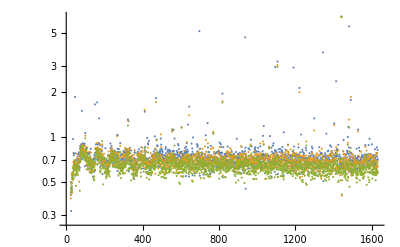

```mathematica
ListLogPlot[{ImageData[debias⟦"R"⟧]⟦64⟧,ImageData[debias⟦"G"⟧]⟦1⟧,ImageData[debias⟦"B"⟧]⟦64⟧}/dnStep,PlotRange->All]
```

## Bright Segments

```mathematica
ssByMinEdge=SortBy[segStats,Min[#⟦"edges"⟧]&];
```

```mathematica
ssByMinEdge⟦{1,-1}⟧
```

{<|edges→{0.,0.,0.,0.},dark→{-0.00276056,-0.0307365},entropyish→5640,energyish→65.5783,entropy→0.33588,energy→0.812088,mean→0.00031088,median→0.000347343,standardDeviation→0.000106469,fileName→/Users/bswift/Downloads/junoDirs/PJ00/JNCE_2016240_00C06162_V02-raw.png,position→{Key[B],5,1},fnPathName→/Users/bswift/Downloads/junoDirs/PJ00/JNCE_2016240_00C06162_V02-raw.png,fnBaseName→JNCE_2016240_00C06162_V02-raw.png,parsedOK→True,fnDate→2016240,fnOrbit→00,fnFilter→C,fnIndex→06162,fnVersion→02,fnRest→raw.png,filters→{B,G,R},fnType→raw,pds→False,gzip→False|>,<|edges→{0.274748,0.249739,0.260854,0.263633},dark→{0.441678,0.458946},entropyish→129888,energyish→77790.3,entropy→3.65937,energy→0.032065,mean→0.368772,median→0.388677,standardDeviation→0.073893,fileName→/Users/bswift/Downloads/junoDirs/PJ16/JNCE_2018302_16C00020_V01-raw.png,position→{Key[R],20,1},fnPathName→/Users/bswift/Downloads/junoDirs/PJ16/JNCE_2018302_16C00020_V01-raw.png,fnBaseName→JNCE_2018302_16C00020_V01-raw.png,parsedOK→True,fnDate→2018302,fnOrbit→16,fnFilter→C,fnIndex→00020,fnVersion→01,fnRest→raw.png,filters→{B,G,R},fnType→raw,pds→False,gzip→False|>}

```mathematica
ssByMinEdgeG=Select[ssByMinEdge,#⟦"position",1⟧==Key["G"]&];
```

```mathematica
ssByMinEdgeB=Select[ssByMinEdge,#⟦"position",1⟧==Key["B"]&];
```

```mathematica
ssByMinEdgeR=Select[ssByMinEdge,#⟦"position",1⟧==Key["R"]&];
```

```mathematica
Dimensions/@{ssByMinEdgeR,ssByMinEdgeG,ssByMinEdgeB}
```

{{9434},{9434},{9434}}

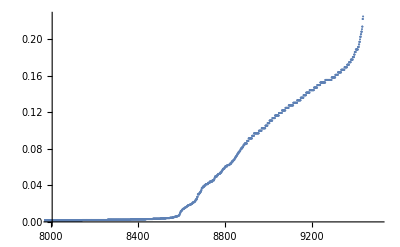

```mathematica
ListPlot[Map[Min[#⟦"edges"⟧]&,ssByMinEdgeG],PlotRange->{{8000,9500},All}]
```

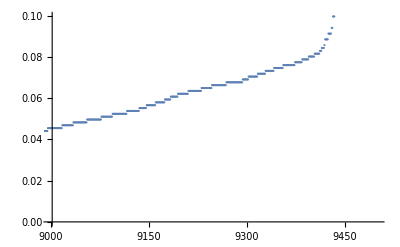

```mathematica
ListPlot[Map[Min[#⟦"edges"⟧]&,ssByMinEdgeB],PlotRange->{{9000,9500},All}]
```

```mathematica
(* Identify orbits with brightest segments.
Will use orbits with enough bright segments to support selection of 30 segments from each oribt for generation of flats. *)
```

```mathematica
edgeOrbitR=Map[ToExpression[#⟦"fnOrbit"⟧]&,ssByMinEdgeR];
```

```mathematica
edgeOrbitG=Map[ToExpression[#⟦"fnOrbit"⟧]&,ssByMinEdgeG];
```

```mathematica
edgeOrbitB=Map[ToExpression[#⟦"fnOrbit"⟧]&,ssByMinEdgeB];
```

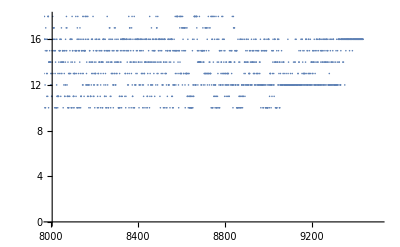

```mathematica
ListPlot[edgeOrbitR,PlotRange->{{8000,9500},All}]
```

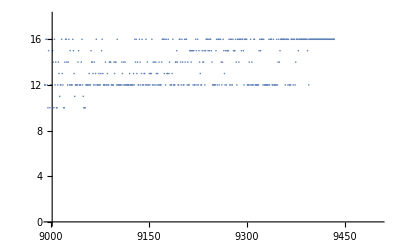

```mathematica
ListPlot[edgeOrbitG,PlotRange->{{9000,9500},All}]
```

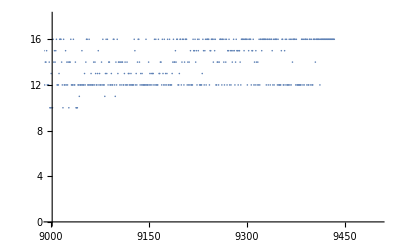

```mathematica
ListPlot[edgeOrbitB,PlotRange->{{9000,9500},All}]
```

```mathematica
Tally[edgeOrbitG⟦9000;;-1⟧]//Sort
```

{{10,8},{11,3},{12,159},{13,30},{14,52},{15,36},{16,147}}

```mathematica
Tally[edgeOrbitB⟦9000;;-1⟧]//Sort
```

{{10,8},{11,3},{12,158},{13,30},{14,50},{15,36},{16,150}}

```mathematica
Tally[edgeOrbitR⟦9000;;-1⟧]//Sort
```

{{10,9},{11,3},{12,158},{13,30},{14,52},{15,35},{16,148}}

```mathematica
ssByMinEdgeR⟦9000⟧
```

<|edges→{0.133032,0.124696,0.194165,0.130254},dark→{0.268241,0.278246},entropyish→165048,energyish→45309.3,entropy→3.87482,energy→0.0230016,mean→0.214793,median→0.221952,standardDeviation→0.0476859,fileName→/Users/bswift/Downloads/junoDirs/PJ16/JNCE_2018302_16C00013_V01-raw.png,position→{Key[R],14,1},fnPathName→/Users/bswift/Downloads/junoDirs/PJ16/JNCE_2018302_16C00013_V01-raw.png,fnBaseName→JNCE_2018302_16C00013_V01-raw.png,parsedOK→True,fnDate→2018302,fnOrbit→16,fnFilter→C,fnIndex→00013,fnVersion→01,fnRest→raw.png,filters→{B,G,R},fnType→raw,pds→False,gzip→False|>

```mathematica
orbForFlats={"12","13","14","15","16"}
```

{12,13,14,15,16}

```mathematica
flatSelectionR=Flatten@Table[RandomSample[Select[ssByMinEdgeR⟦9000;;-1⟧,#⟦"fnOrbit"⟧==orb&],30]
,{orb,orbForFlats}]; (* 30 samples from each of the above orbits, to produced flats that aren't skewed toward orbit 16 *)
```

```mathematica
flatSelectionG=Flatten@Table[RandomSample[Select[ssByMinEdgeG⟦9000;;-1⟧,#⟦"fnOrbit"⟧==orb&],30]
,{orb,orbForFlats}]; (* 30 samples from each of the above orbits, to produced flats that aren't skewed toward orbit 16 *)
```

```mathematica
flatSelectionB=Flatten@Table[RandomSample[Select[ssByMinEdgeB⟦9000;;-1⟧,#⟦"fnOrbit"⟧==orb&],30]
,{orb,orbForFlats}]; (* 30 samples from each of the above orbits, to produced flats that aren't skewed toward orbit 16 *)
```

```mathematica
Dimensions/@{flatSelectionR,flatSelectionG,flatSelectionG}
```

{{150},{150},{150}}

```mathematica
flatSelectionR⟦1⟧
```

<|edges→{0.191386,0.163598,0.244182,0.174713},dark→{0.319394,0.32806},entropyish→178336,energyish→56696.1,entropy→3.82954,energy→0.0253536,mean→0.268773,median→0.283084,standardDeviation→0.0547511,fileName→/Users/bswift/Downloads/junoDirs/PJ12/JNCE_2018091_12C00091_V01-raw.png,position→{Key[R],14,1},fnPathName→/Users/bswift/Downloads/junoDirs/PJ12/JNCE_2018091_12C00091_V01-raw.png,fnBaseName→JNCE_2018091_12C00091_V01-raw.png,parsedOK→True,fnDate→2018091,fnOrbit→12,fnFilter→C,fnIndex→00091,fnVersion→01,fnRest→raw.png,filters→{B,G,R},fnType→raw,pds→False,gzip→False|>

```mathematica
flatSelectionBGR=Join[flatSelectionB,flatSelectionG,flatSelectionR];
```

```mathematica
tbrightImages=selectedStatsToImages[flatSelectionBGR];
```

```mathematica
brightSegsData=Map[ImageData,tbrightImages,{-1}];
```

```mathematica
Map[Dimensions,brightSegsData]
```

<|B→{150,128,1648},G→{150,128,1648},R→{150,128,1648}|>

```mathematica
(* old *)
```

<|B→{166,128,1648},G→{174,128,1648},R→{157,128,1648}|>

```mathematica
(* Trimmed mean of stack of bright framelets, toss two darkest and two brightest values per pixel *)
```

```mathematica
AbsoluteTiming[
Parallelize[
flatData=Map[
Map[
TrimmedMean[#,{2/Length[#],2/Length[#]}]&
,Transpose[#,{3,1,2}],{-2}]&
,brightSegsData]
];
] (* 65 parallel
20 sec, 3x150 segments *)
```

{21.1374,Null}

```mathematica
Dimensions/@flatData
```

<|B→{128,1648},G→{128,1648},R→{128,1648}|>

```mathematica
flatTotals=Map[Total[Flatten[#]]&,flatData]
```

<|B→21071.1,G→51235.4,R→62212.8|>

```mathematica
colorBalance
```

{0.487232,0.408409,0.171693}

```mathematica
Values[flatTotals⟦{"R","G","B"}⟧]/colorBalance
```

{127686.,125451.,122725.}

```mathematica
flatFieldsRough=Map[Image[#,"Real32"]&,flatData] (* "F" , average of bright framelets *)
```

<|B→-Graphics-,G→-Graphics-,R→-Graphics-|>

### Smooth Flats (from FlatFieldInvestigation.nb)

```mathematica
Clear[x,y];
order=10;
polyTerms=Flatten[Table[
Table[
{x^(i-1)y^(j-i)}
,{i,j,1,-1}
]
,{j,order+1,1,-1}
]];
```

```mathematica
polyTerms
```

{x^10,x^9 y,x^8 y^2,x^7 y^3,x^6 y^4,x^5 y^5,x^4 y^6,x^3 y^7,x^2 y^8,x y^9,y^10,x^9,x^8 y,x^7 y^2,x^6 y^3,x^5 y^4,x^4 y^5,x^3 y^6,x^2 y^7,x y^8,y^9,x^8,x^7 y,x^6 y^2,x^5 y^3,x^4 y^4,x^3 y^5,x^2 y^6,x y^7,y^8,x^7,x^6 y,x^5 y^2,x^4 y^3,x^3 y^4,x^2 y^5,x y^6,y^7,x^6,x^5 y,x^4 y^2,x^3 y^3,x^2 y^4,x y^5,y^6,x^5,x^4 y,x^3 y^2,x^2 y^3,x y^4,y^5,x^4,x^3 y,x^2 y^2,x y^3,y^4,x^3,x^2 y,x y^2,y^3,x^2,x y,y^2,x,y,1}

```mathematica
smoothField[img_Image]:=Block[
{},
imgData=ImageData[img];
unTrimmedData=MapIndexed[Join[#2,{#1}]&,imgData,{2}]; (* add indicies *)
trimmedData=unTrimmedData⟦1;;-1,25;;-18⟧;
flatTrimmedData=Flatten[trimmedData,1];
sub1=LinearModelFit[flatTrimmedData,polyTerms,{x,y}];
Print[sub1[{"AdjustedRSquared","RSquared","AIC","BIC"}]];
predictedResponse=sub1["PredictedResponse"];
reshapedPredict=ArrayReshape[predictedResponse,Dimensions[trimmedData]⟦{1,2}⟧];
predictImg=Image[reshapedPredict,"Real32"];
predictImgUntrim=ImageAssemble[{ImageTake[img,{1,-1},{1,24}],predictImg,ImageTake[img,{1,-1},{-17,-1}]}];
predictImgUntrim
]
```

```mathematica
(* img values where fitMask==0 excluded from fit *)
smoothField[img_Image,fitMask_Image]:=Block[
{imgData
,imgW,imgH
,unTrimmedData
,trimmedData
,flatTrimmedData
,sub1
,func
,fitImage
},
Assert[ImageDimensions[img]==ImageDimensions[fitMask]];
{imgW,imgH}=1.0ImageDimensions[img];
imgData=ImageData[img];
unTrimmedData=MapIndexed[Join[#2,{#1}]&,imgData,{2}]; (* add indicies *)
trimmedData=Pick[unTrimmedData,ImageData[fitMask],1];
flatTrimmedData=Flatten[trimmedData,1];
sub1=LinearModelFit[flatTrimmedData,polyTerms,{x,y}];
Print[sub1[{"AdjustedRSquared","RSquared","AIC","BIC"}]];
func=sub1["Function"];
fitImage=Image[Table[func[y,x],{y,1.,imgH},{x,1.,imgW}],"Real32"];
fitImage
]
```

```mathematica
(* mask that selects dark spots and edges of active pixels (values with high gradient) with addition of two pixels of feathering. These values will be transfered to smoothed flat *)
flatMergeMask=MapThread[
Image[
ImageClip[1/3DistanceTransform[Dilation[
Binarize[
GradientFilter[#1,1.4]
,15.#2
]
,2]
]
]
,"Real32"
]&
,{flatFieldsRough,(imageInfo/@Map[GradientFilter[#,1.4]&,flatFieldsRough])⟦All,"Mean"⟧}]
```

<|B→-Graphics-,G→-Graphics-,R→-Graphics-|>

```mathematica
(* Create mask of values to use for fit. Excludes dark spots from above, non-active pixels *)
```

```mathematica
flatFitSpotsMask=Map[ColorNegate[Binarize[#,0]]&,flatMergeMask]
```

<|B→-Graphics-,G→-Graphics-,R→-Graphics-|>

```mathematica
flatFitMask=Map[ReplacePixelValue[#,{{1;;24,All},{1648-17+1;;1648,All}}->0]&,flatFitSpotsMask] (* remove non-active pixels from edges of mask *)
```

<|B→-Graphics-,G→-Graphics-,R→-Graphics-|>

```mathematica
{flatFieldsRough,flatFitMask}
```

{<|B→-Graphics-,G→-Graphics-,R→-Graphics-|>,<|B→-Graphics-,G→-Graphics-,R→-Graphics-|>}

```mathematica
flatFieldsFit=MapThread[smoothField,{flatFieldsRough,flatFitMask}]
```

{0.999008,0.999009,-2.58718×10^6,-2.58649×10^6}

{0.99844,0.99844,-2.19714×10^6,-2.19645×10^6}

{0.997959,0.99796,-2.02965×10^6,-2.02897×10^6}

<|B→-Graphics-,G→-Graphics-,R→-Graphics-|>

```mathematica
Map[ImageAdjust,flatFieldsRough]
```

<|B→-Graphics-,G→-Graphics-,R→-Graphics-|>

```mathematica
(* old *)
```

<|B→-Graphics-,G→-Graphics-,R→-Graphics-|>

```mathematica
colorBalance⟦{3,2,1}⟧
```

{0.171693,0.408409,0.487232}

```mathematica
MapThread[ImageAdjust[#,{0,0,1},{0,#2}]&,{flatFieldsRough,AssociationThread[{"B","G","R"}-> colorBalance⟦{3,2,1}⟧]}]
```

<|B→-Graphics-,G→-Graphics-,R→-Graphics-|>

```mathematica
(* merge the dark spots from the flatFieldsRough with the flatFieldsFit *)
flatFields=((flatFieldsRough flatMergeMask)+ (flatFieldsFit (1-flatMergeMask)))
```

<|B→-Graphics-,G→-Graphics-,R→-Graphics-|>

```mathematica
MapThread[ImageAdjust[#,{0,0,1},{0,#2}]&,{flatFields,AssociationThread[{"B","G","R"}-> colorBalance⟦{3,2,1}⟧]}]
```

<|B→-Graphics-,G→-Graphics-,R→-Graphics-|>

```mathematica
(**)
```

<|B→-Graphics-,G→-Graphics-,R→-Graphics-|>

```mathematica
Map[imageInfo,flatFieldsRough-flatFieldsFit]
```

<|B→<|Channels→1,ColorSpace→Automatic,DataRange→{0.,1.},DataType→Real32,Dimensions→{128,1648},SampleDepth→32,Transparency→False,Min→-0.0978502,Max→0.00522377,Mean→-0.0020713,Median→5.58794×10^-7,StandardDeviation→0.0131795|>,G→<|Channels→1,ColorSpace→Automatic,DataRange→{0.,1.},DataType→Real32,Dimensions→{128,1648},SampleDepth→32,Transparency→False,Min→-0.230518,Max→0.0240484,Mean→-0.00505071,Median→-0.0000145584,StandardDeviation→0.0320421|>,R→<|Channels→1,ColorSpace→Automatic,DataRange→{0.,1.},DataType→Real32,Dimensions→{128,1648},SampleDepth→32,Transparency→False,Min→-0.278697,Max→0.0099721,Mean→-0.00597918,Median→-0.0000377744,StandardDeviation→0.0379124|>|>

```mathematica
MapThread[ImageAdjust[#1,{0,0,1},8 #2{-1,1}]&,{flatFieldsRough-flatFieldsFit,Map[imageInfo,Map[ImageTake[#,All,{24,-18}]&,flatFieldsRough-flatFieldsFit]]⟦All,"StandardDeviation"⟧}]
```

<|B→-Graphics-,G→-Graphics-,R→-Graphics-|>

```mathematica
MapThread[ImageAdjust[#1,{0,0,1},8 #2{-1,1}]&,{flatFieldsRough-flatFields,Map[imageInfo,Map[ImageTake[#,All,{24,-18}]&,flatFieldsRough-flatFieldsFit]]⟦All,"StandardDeviation"⟧}]
```

<|B→-Graphics-,G→-Graphics-,R→-Graphics-|>

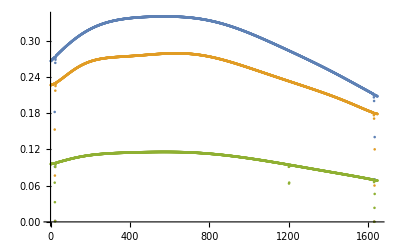

```mathematica
ListPlot[{ImageData[flatFields⟦"R"⟧]⟦64⟧,ImageData[flatFields⟦"G"⟧]⟦1⟧,ImageData[flatFields⟦"B"⟧]⟦64⟧}(*/dnStep*),PlotRange->All]
```

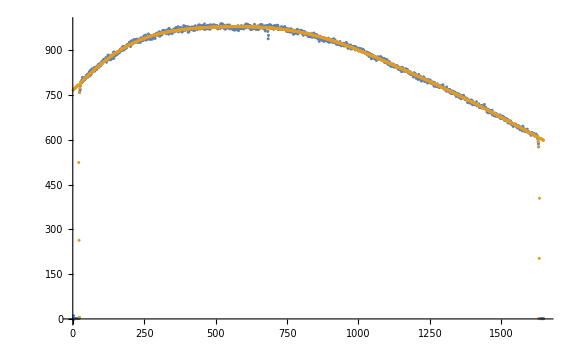
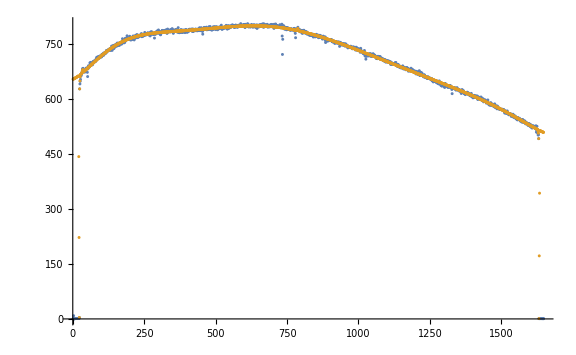
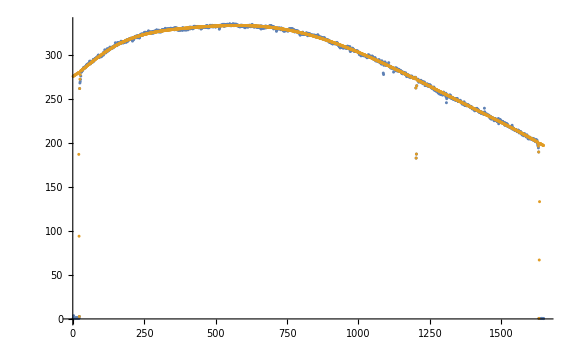

```mathematica
Table[ListPlot[{ImageData[flatFieldsRough⟦color⟧]⟦64⟧,ImageData[flatFields⟦color⟧]⟦64⟧}/dnStep,PlotRange->All,ImageSize->Large]
,{color,{"R","G","B"}}]
```

### Residual Signal Investigation

```mathematica
(* determin that higher order fit needed to match residual shape of flat *)
```

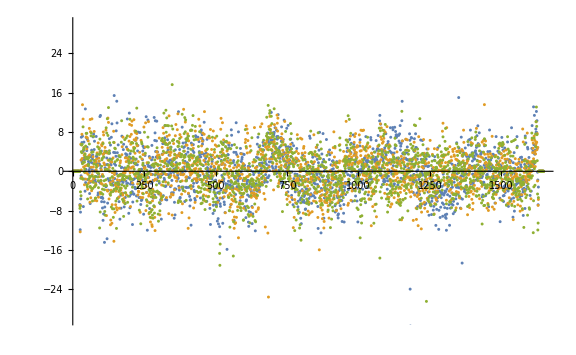
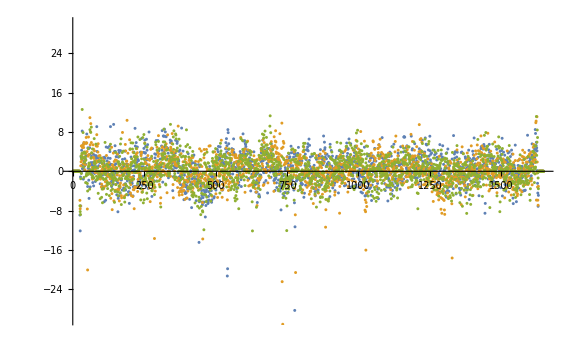
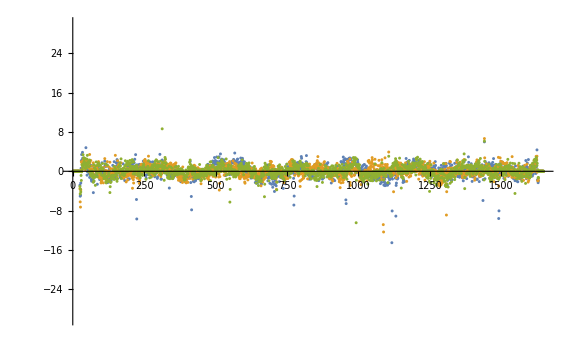

```mathematica
Table[ListPlot[Table[(ImageData[flatFieldsRough⟦color⟧]⟦cut⟧-ImageData[flatFields⟦color⟧]⟦cut⟧)/dnStep,{cut,{16,64,112}}],PlotRange->{All,{-30,30}},ImageSize->Large]
,{color,{"R","G","B"}}]
```

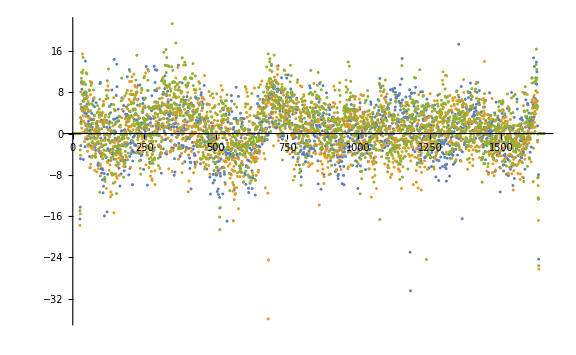
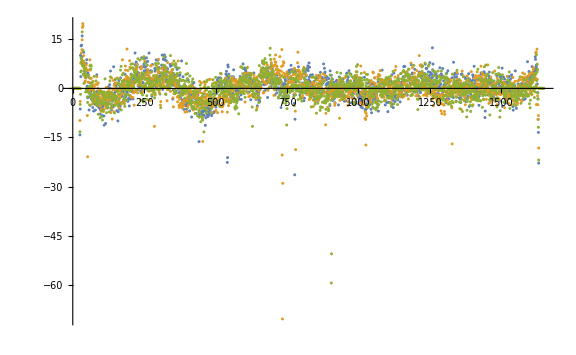
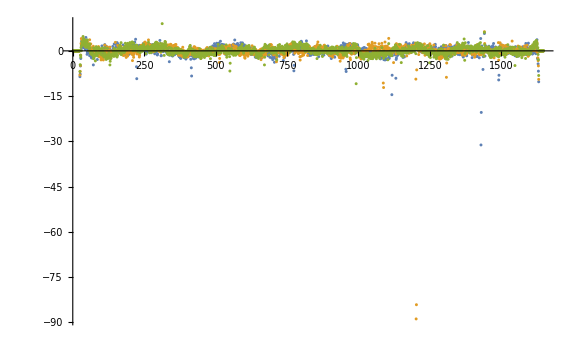

```mathematica
(* order 7 {"12","13","14","15","16"} *)
```

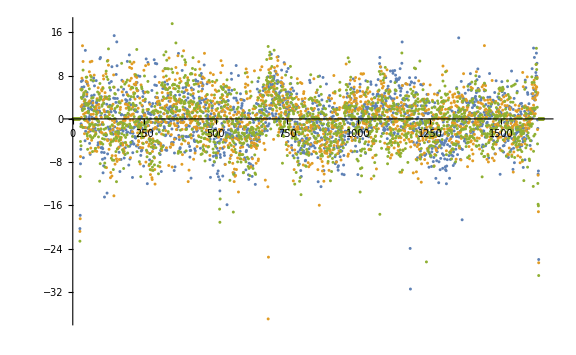
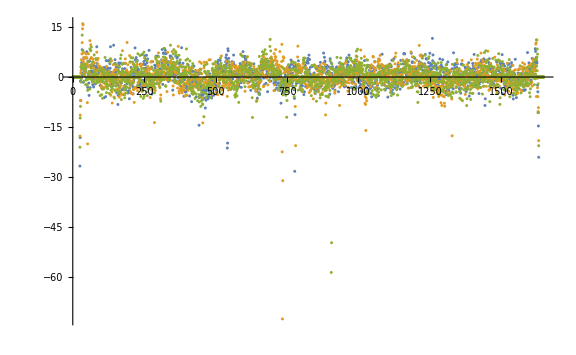
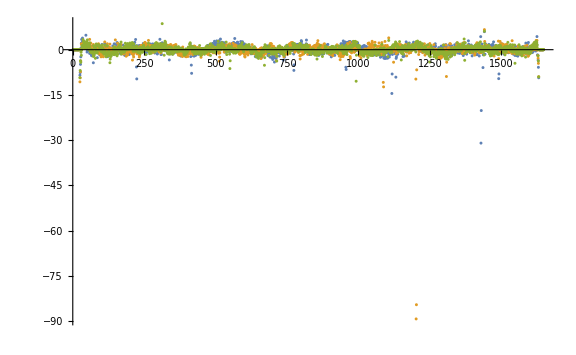

```mathematica
(* order 10 {"12","13","14","15","16"} *)
```

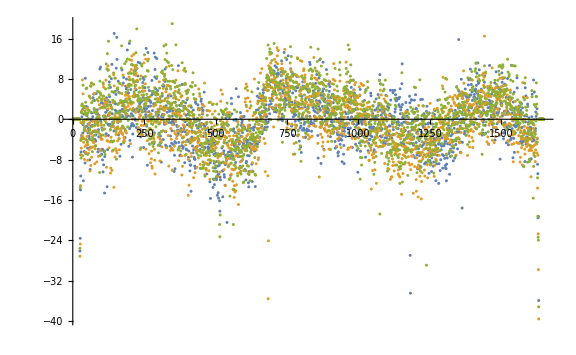
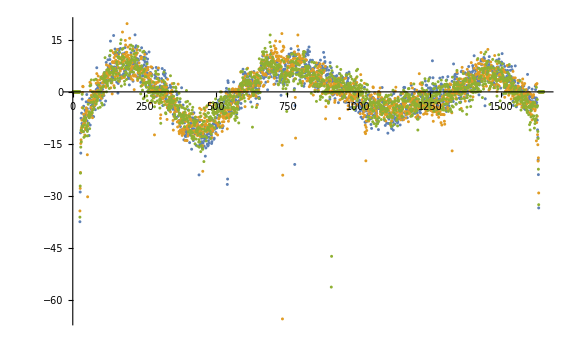
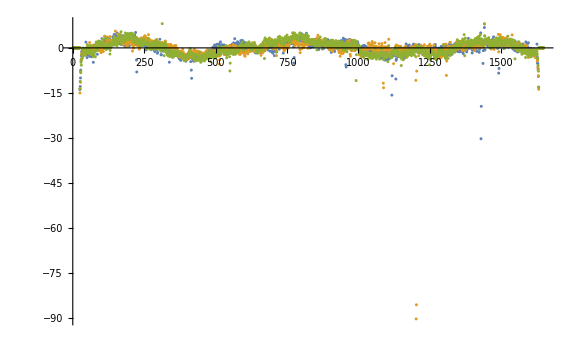

```mathematica
(* order 5 {"12","13","14","15","16"} *)
```

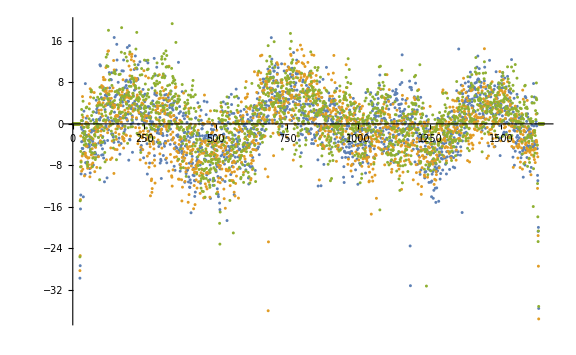
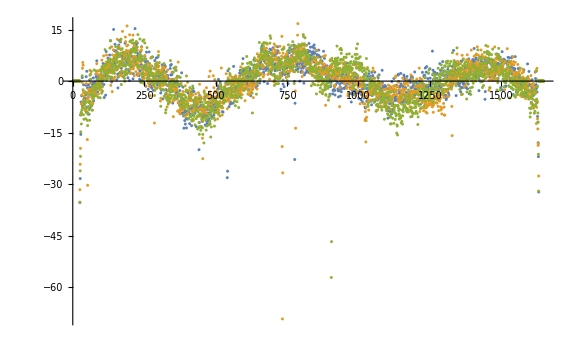
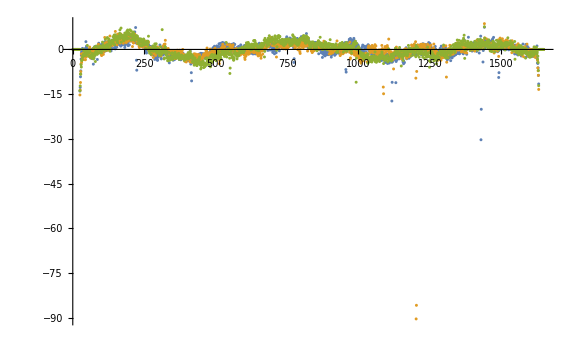

```mathematica
(* {"13","14","15","16"} *)
```

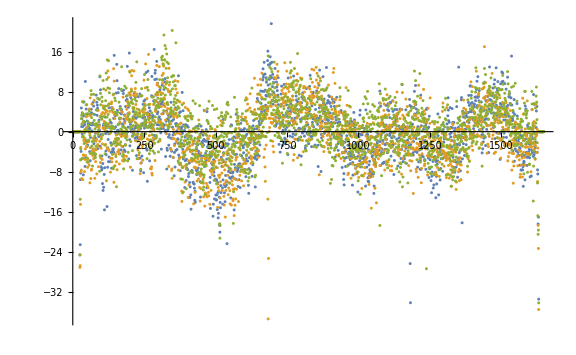
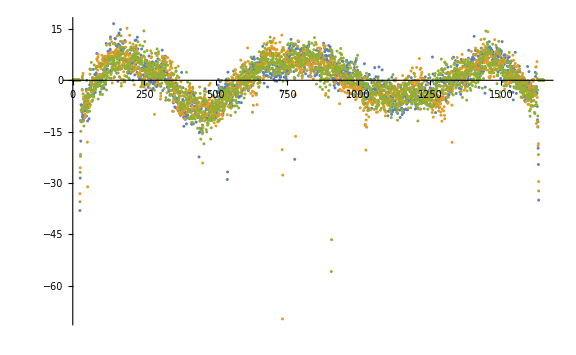
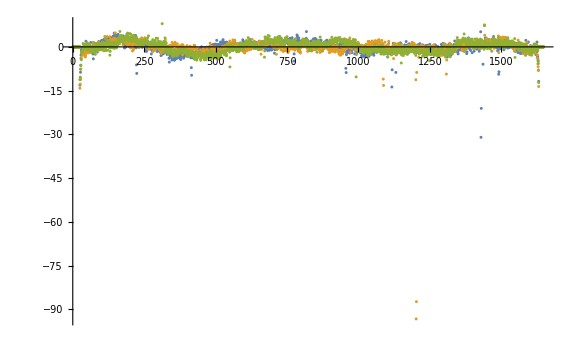

```mathematica
(* {"12","14","15","16"} *)
```

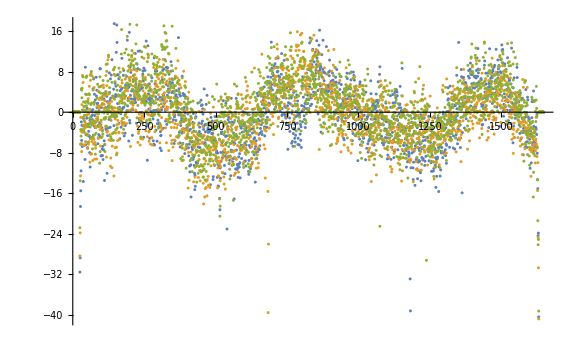
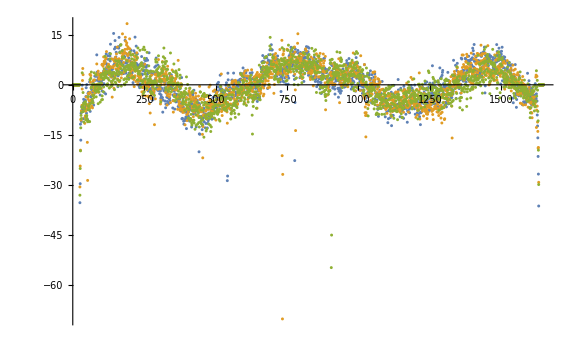
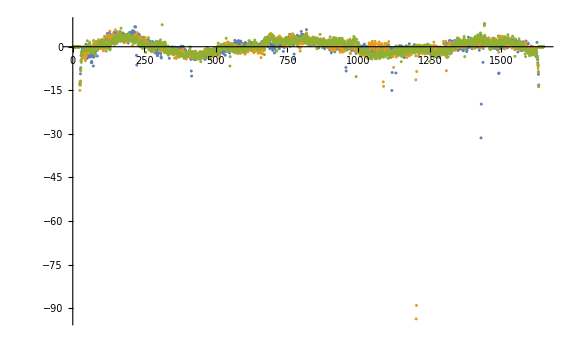

```mathematica
(* {"12","13","15","16"} *)
```

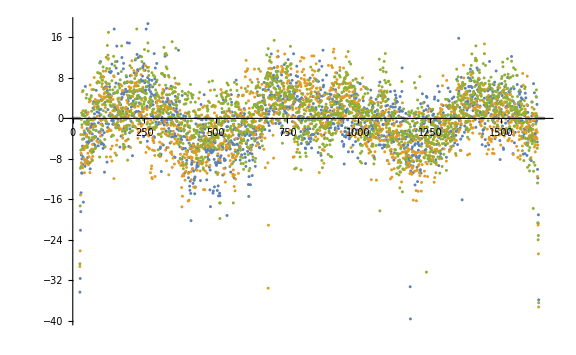
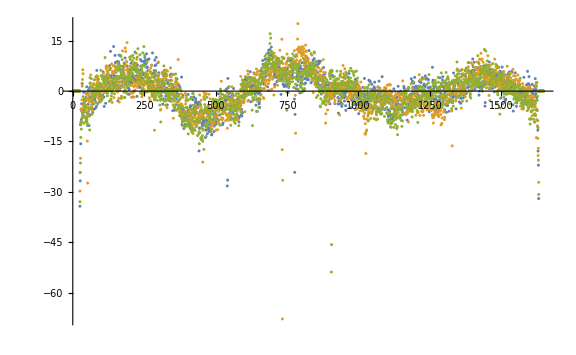
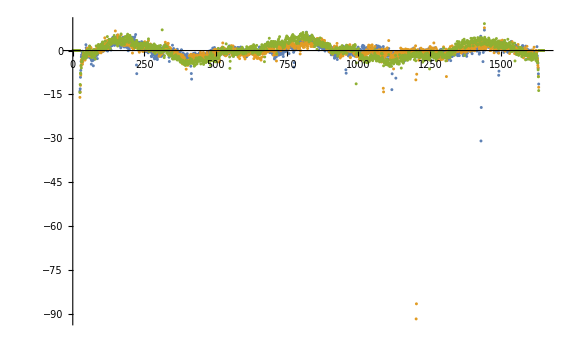

```mathematica
(* {"12","13","14","16"} *)
```

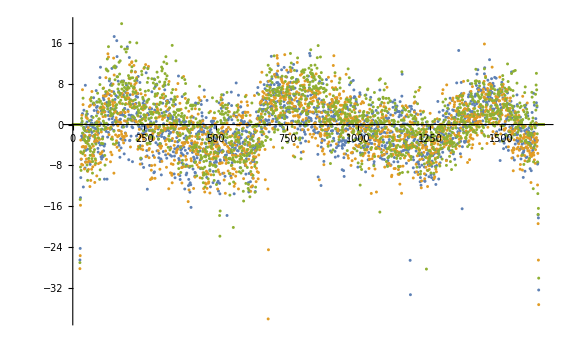
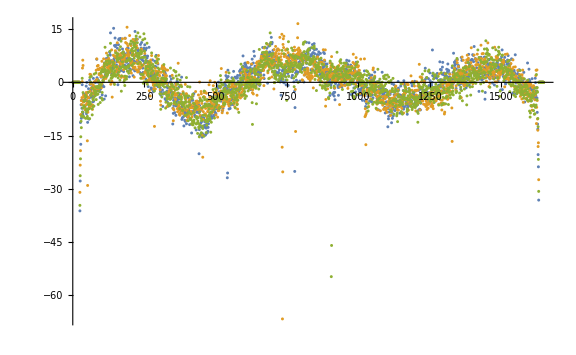
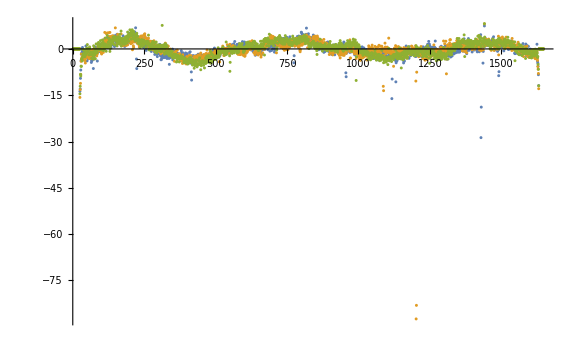

```mathematica
(* {"12","13","14","15"} *)
```

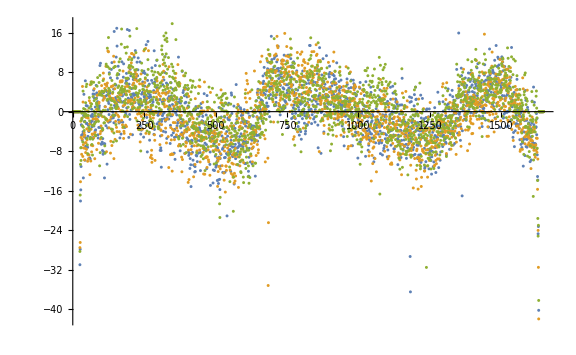
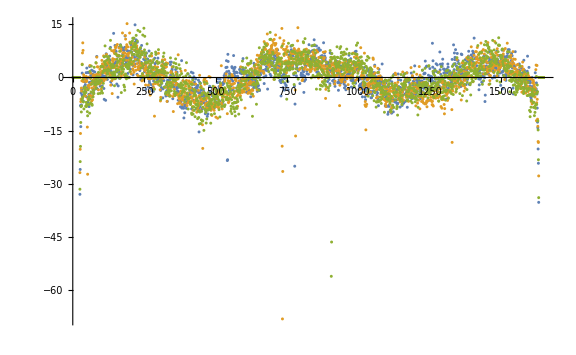
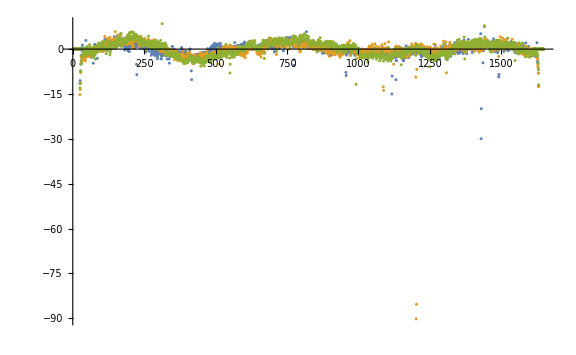

```mathematica
(* {"12","13","14","15","16"} *)
```

### Cont.

```mathematica
(* old *)
```

```mathematica
(* F - D *)(* flat - debias *)
fmd=MapThread[ImageSubtract[#1, #2]&,{flatFields,debias}]
```

<|B→-Graphics-,G→-Graphics-,R→-Graphics-|>

```mathematica
Map[imageInfo,debias]
```

<|B→<|Channels→1,ColorSpace→Automatic,DataRange→{0.,1.},DataType→Real32,Dimensions→{128,1648},SampleDepth→32,Transparency→False,Min→0.,Max→0.00553819,Mean→0.000220398,Median→0.000220707,StandardDeviation→0.000070425|>,G→<|Channels→1,ColorSpace→Automatic,DataRange→{0.,1.},DataType→Real32,Dimensions→{128,1648},SampleDepth→32,Transparency→False,Min→0.,Max→0.0210118,Mean→0.000243352,Median→0.000242416,StandardDeviation→0.0000954898|>,R→<|Channels→1,ColorSpace→Automatic,DataRange→{0.,1.},DataType→Real32,Dimensions→{128,1648},SampleDepth→32,Transparency→False,Min→0.,Max→0.0100392,Mean→0.000251162,Median→0.000246034,StandardDeviation→0.000107438|>|>

```mathematica
Map[imageInfo,fmd]
```

<|B→<|Channels→1,ColorSpace→Automatic,DataRange→{0.,1.},DataType→Real32,Dimensions→{128,1648},SampleDepth→32,Transparency→False,Min→0.000135606,Max→0.117666,Mean→0.101522,Median→0.10681,StandardDeviation→0.0146725|>,G→<|Channels→1,ColorSpace→Automatic,DataRange→{0.,1.},DataType→Real32,Dimensions→{128,1648},SampleDepth→32,Transparency→False,Min→0.000264076,Max→0.297022,Mean→0.247165,Median→0.257782,StandardDeviation→0.0311182|>,R→<|Channels→1,ColorSpace→Automatic,DataRange→{0.,1.},DataType→Real32,Dimensions→{128,1648},SampleDepth→32,Transparency→False,Min→0.000349722,Max→0.346164,Mean→0.300019,Median→0.313457,StandardDeviation→0.0407773|>|>

```mathematica
meanOfFmD=Map[ImageMeasurements[
ImageTake[#,All,{24,-18}] (* exclude header/trailer *)
,"Mean"
]&,fmd] (* "m", image mean of F - D *)
```

<|B→0.102145,G→0.248675,R→0.302|>

```mathematica
<|"B"->0.1054112049140853,"G"->0.251418549639207,"R"->0.29611770781641766|> (* old *)
```

<|B→0.105411,G→0.251419,R→0.296118|>

```mathematica
Values[meanOfFmD⟦{"R","G","B"}⟧]/colorBalance
```

{0.619828,0.608888,0.594925}

```mathematica
Map[imageInfo,flatFields]
```

<|B→<|Channels→1,ColorSpace→Automatic,DataRange→{0.,1.},DataType→Real,Dimensions→{128,1648},SampleDepth→64,Transparency→False,Min→0.000135606,Max→0.117877,Mean→0.101742,Median→0.107028,StandardDeviation→0.0146846|>,G→<|Channels→1,ColorSpace→Automatic,DataRange→{0.,1.},DataType→Real,Dimensions→{128,1648},SampleDepth→64,Transparency→False,Min→0.000264076,Max→0.297297,Mean→0.247408,Median→0.258024,StandardDeviation→0.0311308|>,R→<|Channels→1,ColorSpace→Automatic,DataRange→{0.,1.},DataType→Real,Dimensions→{128,1648},SampleDepth→64,Transparency→False,Min→0.000349722,Max→0.346391,Mean→0.30027,Median→0.31373,StandardDeviation→0.0407889|>|>

```mathematica
Map[imageInfo,fmd]
```

<|B→<|Channels→1,ColorSpace→Automatic,DataRange→{0.,1.},DataType→Real,Dimensions→{128,1648},SampleDepth→64,Transparency→False,Min→0.000135606,Max→0.117666,Mean→0.101522,Median→0.10681,StandardDeviation→0.0146725|>,G→<|Channels→1,ColorSpace→Automatic,DataRange→{0.,1.},DataType→Real,Dimensions→{128,1648},SampleDepth→64,Transparency→False,Min→0.000264076,Max→0.297022,Mean→0.247165,Median→0.257782,StandardDeviation→0.0311182|>,R→<|Channels→1,ColorSpace→Automatic,DataRange→{0.,1.},DataType→Real,Dimensions→{128,1648},SampleDepth→64,Transparency→False,Min→0.000349722,Max→0.346164,Mean→0.300019,Median→0.313457,StandardDeviation→0.0407773|>|>

```mathematica
(* gain=m/(F-D)
*)
gain=MapThread[Function[{mValue,fmdImage},
ImagePad[
ImageApply[mValue/#&,ImageTake[fmdImage,All,{24,-18}]]
,{{24,18}-1,{0,0}},1.0
]
]
,{meanOfFmD,fmd}]
```

<|B→-Graphics-,G→-Graphics-,R→-Graphics-|>

```mathematica
Map[imageInfo,gain]
```

<|B→<|Channels→1,ColorSpace→Automatic,DataRange→{0.,1.},DataType→Real,Dimensions→{128,1648},SampleDepth→64,Transparency→False,Min→0.868093,Max→2.2792,Mean→1.02071,Median→0.956319,StandardDeviation→0.157224|>,G→<|Channels→1,ColorSpace→Automatic,DataRange→{0.,1.},DataType→Real,Dimensions→{128,1648},SampleDepth→64,Transparency→False,Min→0.837229,Max→3.01282,Mean→1.01461,Median→0.964671,StandardDeviation→0.130046|>,R→<|Channels→1,ColorSpace→Automatic,DataRange→{0.,1.},DataType→Real,Dimensions→{128,1648},SampleDepth→64,Transparency→False,Min→0.872421,Max→4.97336,Mean→1.01761,Median→0.963449,StandardDeviation→0.144167|>|>

```mathematica
(*old*)
```

<|B→<|Channels→1,ColorSpace→Automatic,DataRange→{0.,1.},DataType→Real32,Dimensions→{128,1648},SampleDepth→32,Transparency→False,Min→0.8689,Max→2.32362,Mean→1.01204,Median→0.977712,StandardDeviation→0.115747|>,G→<|Channels→1,ColorSpace→Automatic,DataRange→{0.,1.},DataType→Real32,Dimensions→{128,1648},SampleDepth→32,Transparency→False,Min→0.845741,Max→3.34308,Mean→1.0107,Median→0.97847,StandardDeviation→0.108959|>,R→<|Channels→1,ColorSpace→Automatic,DataRange→{0.,1.},DataType→Real32,Dimensions→{128,1648},SampleDepth→32,Transparency→False,Min→0.861149,Max→5.24375,Mean→1.01263,Median→0.974672,StandardDeviation→0.119011|>|>

```mathematica
debias
```

<|B→-Graphics-,G→-Graphics-,R→-Graphics-|>

#### Test Correction

```mathematica
(* C=(R-D)G *)
flatFieldCorrect[rawFramlet_Image,chanKey_]:= ImageMultiply[
ImageSubtract[rawFramlet,debias⟦chanKey⟧],gain⟦chanKey⟧]
```

```mathematica
framelet
```

-Graphics-

```mathematica
flatFieldCorrect[framelet,"R"]
```

-Graphics-

```mathematica
(*old*)
```

-Graphics-

#### Highlight Filter Defects

```mathematica
subFlats=Map[
ImageTake[
ImageSubtract[#,ImageMultiply[GaussianFilter[#,25],1]]
,All,{24,-18}]
&,flatFieldsRough]
```

<|B→-Graphics-,G→-Graphics-,R→-Graphics-|>

```mathematica
Map[ImageAdjust[#
,{0,0,1/2},Sort[Flatten[ImageData[#]]]⟦{Round[.001 pixelsInFramelet],Round[-.02 pixelsInFramelet]}⟧
]&,subFlats]
```

<|B→-Graphics-,G→-Graphics-,R→-Graphics-|>

```mathematica
(* old *)
```

<|B→-Graphics-,G→-Graphics-,R→-Graphics-|>

#### New Color Balance

```mathematica
fmd=<|"B"->-Graphics-,"G"->-Graphics-,"R"->-Graphics-|>
```

<|B→-Graphics-,G→-Graphics-,R→-Graphics-|>

```mathematica
Map[imageInfo,fmd]
```

<|B→<|Channels→1,ColorSpace→Automatic,DataRange→{0.,1.},DataType→Real32,Dimensions→{128,1648},SampleDepth→32,Transparency→False,Min→0.0000370499,Max→0.120449,Mean→0.101699,Median→0.107677,StandardDeviation→0.0199901|>,G→<|Channels→1,ColorSpace→Automatic,DataRange→{0.,1.},DataType→Real32,Dimensions→{128,1648},SampleDepth→32,Transparency→False,Min→0.0000391048,Max→0.296609,Mean→0.242088,Median→0.25612,StandardDeviation→0.0465813|>,R→<|Channels→1,ColorSpace→Automatic,DataRange→{0.,1.},DataType→Real32,Dimensions→{128,1648},SampleDepth→32,Transparency→False,Min→0.000038343,Max→0.341096,Mean→0.287858,Median→0.305575,StandardDeviation→0.057101|>|>

```mathematica
Map[ImageAdjust,fmd]
```

<|B→-Graphics-,G→-Graphics-,R→-Graphics-|>

```mathematica
cb2=Map[TrimmedMean[Flatten[ImageData[#]],{.49,.49}]&,fmd] (* mean of middle 2%. Looks like could have just used Median. *)
```

<|B→0.107678,G→0.256134,R→0.305568|>

```mathematica
(*old*)
```

<|B→0.107678,G→0.256134,R→0.305568|>

```mathematica
colorBalance
```

{0.487232,0.408409,0.171693}

```mathematica
cbRatios=Values[cb2⟦{"R","G","B"}⟧]/colorBalance
```

{0.62715,0.62715,0.62715}

```mathematica
colorBalanceFlats=Values[cb2⟦{"R","G","B"}⟧]/Min[cbRatios]
```

{0.487232,0.408409,0.171693}

```mathematica
flatFields
```

<|B→-Graphics-,G→-Graphics-,R→-Graphics-|>

```mathematica
cb3=Map[TrimmedMean[Flatten[ImageData[#]],{.49,.49}]&,flatFields]
```

<|B→0.107027,G→0.258023,R→0.313725|>

```mathematica
Values[cb3⟦{"R","G","B"}⟧]/colorBalance
```

{0.643892,0.631777,0.623359}

```mathematica
gain
```

<|B→-Graphics-,G→-Graphics-,R→-Graphics-|>

```mathematica
cb4=Map[TrimmedMean[Flatten[ImageData[#]],{.49,.49}]&,gain]
```

<|B→0.95637,G→0.964675,R→0.96345|>

```mathematica
Values[cb4⟦{"R","G","B"}⟧]/colorBalance
```

{1.97739,2.36203,5.57022}

#### To do

```mathematica
(* todo

Generate PJ14 vr movie
look at auto estimation (correlation) of spin rate to inter frame delay metadata
Merge changes into Juno28
Post to github
Post to mission juno
*)
```

## Not Evaluated

### Compare New to Old

```mathematica
gainDiff=MapThread[ImageDifference,{gain11to14,gain11to14to18}]
```

```mathematica
Map[imageInfo,gainDiff]
```

```mathematica
Map[ImageAdjust,gainDiff]
```

#### Metrics Review

```mathematica
allEdges // Dimensions
```

```mathematica
mergedEnergy=Merge[Map[#⟦"energy"⟧&,allEdges,{3}],Flatten[#,1]&];
```

```mathematica
mergedEnergyish=Merge[Map[#⟦"energyish"⟧&,allEdges,{3}],Flatten[#,1]&];
```

```mathematica
mergedEnergy//Dimensions
```

```mathematica
mergedEnergy⟦3⟧//Dimensions
```

```mathematica
mergedEnergyish⟦3⟧//Dimensions
```

```mathematica
MapThread[ListPlot[Transpose[{#1,#2}]]&,{mergedEnergy,mergedEnergyish}]
```

```mathematica
Map[ListPlot[Sort[#]]&,mergedEnergy]
```

```mathematica
Map[ListPlot[Sort[#]]&,mergedEnergyish]
```

```mathematica
mergedEntropy=Merge[Map[#⟦"entropy"⟧&,allEdges,{3}],Flatten[#,1]&];
```

```mathematica
mergedEntropyish=Merge[Map[#⟦"entropyish"⟧&,allEdges,{3}],Flatten[#,1]&];
```

```mathematica
MapThread[ListPlot[Transpose[{#1,#2}]]&,{mergedEntropy,mergedEntropyish}]
```

```mathematica
MapThread[ListPlot[Transpose[{Log[#1],#2}]]&,{mergedEntropy,mergedEntropyish}]
```

```mathematica
Map[ListPlot[Sort[#]]&,mergedEntropy]
```

```mathematica
Map[ListPlot[Sort[#]]&,mergedEntropyish]
```

#### Files Used

```mathematica
filesToProcess
```

{/Users/bswift/Downloads/junoDirs/PJ00/JNCE_2016240_00C06162_V02-raw.png,/Users/bswift/Downloads/junoDirs/PJ00/JNCE_2016240_00C06164_V02-raw.png,/Users/bswift/Downloads/junoDirs/PJ00/JNCE_2016240_00C06180_V02-raw.png,/Users/bswift/Downloads/junoDirs/PJ00/JNCE_2016240_00C06184_V02-raw.png,/Users/bswift/Downloads/junoDirs/PJ08/JNCE_2017244_08C00092_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ10/JNCE_2017350_10C00002_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ10/JNCE_2017350_10C00013_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ10/JNCE_2017350_10C00015_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ10/JNCE_2017350_10C00016_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ10/JNCE_2017350_10C00017_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ10/JNCE_2017350_10C00018_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ10/JNCE_2017350_10C00020_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ10/JNCE_2017350_10C00021_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ10/JNCE_2017350_10C00022_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ10/JNCE_2017350_10C00023_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ10/JNCE_2017350_10C00024_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ10/JNCE_2017350_10C00025_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ10/JNCE_2017350_10C00026_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ10/JNCE_2017350_10C00027_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ10/JNCE_2017350_10C00028_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ10/JNCE_2017350_10C00030_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ10/JNCE_2017350_10C00031_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ10/JNCE_2017350_10C00032_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ10/JNCE_2017350_10C00033_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ10/JNCE_2017350_10C00034_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ10/JNCE_2017350_10C00036_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ10/JNCE_2017350_10C00037_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ10/JNCE_2017350_10C00038_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ10/JNCE_2017350_10C00039_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ10/JNCE_2017350_10C00040_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ10/JNCE_2017350_10C00041_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ10/JNCE_2017350_10C00042_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ10/JNCE_2017350_10C00044_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ10/JNCE_2017350_10C00045_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ10/JNCE_2017350_10C00046_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ10/JNCE_2017350_10C00047_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ10/JNCE_2017350_10C00048_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ10/JNCE_2017350_10C00049_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ10/JNCE_2017350_10C00050_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ10/JNCE_2017350_10C00051_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ11/JNCE_2018038_11C00001_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ11/JNCE_2018038_11C00003_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ11/JNCE_2018038_11C00004_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ11/JNCE_2018038_11C00006_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ11/JNCE_2018038_11C00009_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ11/JNCE_2018038_11C00010_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ11/JNCE_2018038_11C00011_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ11/JNCE_2018038_11C00012_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ11/JNCE_2018038_11C00013_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ11/JNCE_2018038_11C00014_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ11/JNCE_2018038_11C00015_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ11/JNCE_2018038_11C00016_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ11/JNCE_2018038_11C00017_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ11/JNCE_2018038_11C00019_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ11/JNCE_2018038_11C00020_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ11/JNCE_2018038_11C00021_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ11/JNCE_2018038_11C00022_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ11/JNCE_2018038_11C00023_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ11/JNCE_2018038_11C00024_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ11/JNCE_2018038_11C00025_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ11/JNCE_2018038_11C00026_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ11/JNCE_2018038_11C00027_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ11/JNCE_2018038_11C00028_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ11/JNCE_2018038_11C00029_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ11/JNCE_2018038_11C00030_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ11/JNCE_2018038_11C00031_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ11/JNCE_2018038_11C00032_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ11/JNCE_2018038_11C00035_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ11/JNCE_2018038_11C00040_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ11/JNCE_2018038_11C00041_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ11/JNCE_2018038_11C00042_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ11/JNCE_2018038_11C00043_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ11/JNCE_2018038_11C00045_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ11/JNCE_2018038_11C00046_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ11/JNCE_2018038_11C00047_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ11/JNCE_2018038_11C00049_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ12/JNCE_2018091_12C00071_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ12/JNCE_2018091_12C00073_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ12/JNCE_2018091_12C00074_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ12/JNCE_2018091_12C00075_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ12/JNCE_2018091_12C00080_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ12/JNCE_2018091_12C00081_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ12/JNCE_2018091_12C00082_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ12/JNCE_2018091_12C00084_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ12/JNCE_2018091_12C00085_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ12/JNCE_2018091_12C00086_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ12/JNCE_2018091_12C00087_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ12/JNCE_2018091_12C00088_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ12/JNCE_2018091_12C00089_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ12/JNCE_2018091_12C00090_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ12/JNCE_2018091_12C00091_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ12/JNCE_2018091_12C00092_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ12/JNCE_2018091_12C00093_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ12/JNCE_2018091_12C00094_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ12/JNCE_2018091_12C00099_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ12/JNCE_2018091_12C00100_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ12/JNCE_2018091_12C00101_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ12/JNCE_2018091_12C00102_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ12/JNCE_2018091_12C00109_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ12/JNCE_2018091_12C00110_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ13/JNCE_2018144_13C00001_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ13/JNCE_2018144_13C00003_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ13/JNCE_2018144_13C00005_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ13/JNCE_2018144_13C00007_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ13/JNCE_2018144_13C00009_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ13/JNCE_2018144_13C00011_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ13/JNCE_2018144_13C00021_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ13/JNCE_2018144_13C00023_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ13/JNCE_2018144_13C00024_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ13/JNCE_2018144_13C00025_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ13/JNCE_2018144_13C00026_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ13/JNCE_2018144_13C00027_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ13/JNCE_2018144_13C00028_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ13/JNCE_2018144_13C00029_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ13/JNCE_2018144_13C00030_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ13/JNCE_2018144_13C00031_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ13/JNCE_2018144_13C00035_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ13/JNCE_2018144_13C00036_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ13/JNCE_2018144_13C00037_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ13/JNCE_2018144_13C00038_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ13/JNCE_2018144_13C00040_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ13/JNCE_2018144_13C00041_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ13/JNCE_2018144_13C00042_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ13/JNCE_2018144_13C00043_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ13/JNCE_2018144_13C00044_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ13/JNCE_2018144_13C00045_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ13/JNCE_2018144_13C00046_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ13/JNCE_2018144_13C00047_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ13/JNCE_2018144_13C00048_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ13/JNCE_2018144_13C00063_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ13/JNCE_2018144_13C00065_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ14/JNCE_2018197_14C00017_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ14/JNCE_2018197_14C00018_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ14/JNCE_2018197_14C00019_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ14/JNCE_2018197_14C00020_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ14/JNCE_2018197_14C00021_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ14/JNCE_2018197_14C00022_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ14/JNCE_2018197_14C00023_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ14/JNCE_2018197_14C00024_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ14/JNCE_2018197_14C00025_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ14/JNCE_2018197_14C00026_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ14/JNCE_2018197_14C00028_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ14/JNCE_2018197_14C00030_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ14/JNCE_2018197_14C00031_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ14/JNCE_2018197_14C00032_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ14/JNCE_2018197_14C00033_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ14/JNCE_2018197_14C00034_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ14/JNCE_2018197_14C00035_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ14/JNCE_2018197_14C00036_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ14/JNCE_2018197_14C00037_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ14/JNCE_2018197_14C00038_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ14/JNCE_2018197_14C00039_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ14/JNCE_2018197_14C00052_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ15/JNCE_2018250_15C00006_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ15/JNCE_2018250_15C00017_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ15/JNCE_2018250_15C00018_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ15/JNCE_2018250_15C00019_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ15/JNCE_2018250_15C00020_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ15/JNCE_2018250_15C00021_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ15/JNCE_2018250_15C00022_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ15/JNCE_2018250_15C00023_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ15/JNCE_2018250_15C00024_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ15/JNCE_2018250_15C00025_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ15/JNCE_2018250_15C00026_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ15/JNCE_2018250_15C00027_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ15/JNCE_2018250_15C00028_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ15/JNCE_2018250_15C00029_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ15/JNCE_2018250_15C00030_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ15/JNCE_2018250_15C00031_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ15/JNCE_2018250_15C00032_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ15/JNCE_2018250_15C00033_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ15/JNCE_2018250_15C00034_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ15/JNCE_2018250_15C00035_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ15/JNCE_2018250_15C00036_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ15/JNCE_2018250_15C00037_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ15/JNCE_2018250_15C00038_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ15/JNCE_2018250_15C00039_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ15/JNCE_2018250_15C00040_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ15/JNCE_2018250_15C00041_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ15/JNCE_2018250_15C00043_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ15/JNCE_2018250_15C00058_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ16/JNCE_2018302_16C00001_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ16/JNCE_2018302_16C00010_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ16/JNCE_2018302_16C00011_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ16/JNCE_2018302_16C00012_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ16/JNCE_2018302_16C00013_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ16/JNCE_2018302_16C00014_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ16/JNCE_2018302_16C00015_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ16/JNCE_2018302_16C00016_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ16/JNCE_2018302_16C00017_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ16/JNCE_2018302_16C00018_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ16/JNCE_2018302_16C00019_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ16/JNCE_2018302_16C00020_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ16/JNCE_2018302_16C00021_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ16/JNCE_2018302_16C00022_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ16/JNCE_2018302_16C00023_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ16/JNCE_2018302_16C00024_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ16/JNCE_2018302_16C00025_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ16/JNCE_2018302_16C00026_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ16/JNCE_2018302_16C00027_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ16/JNCE_2018302_16C00028_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ16/JNCE_2018302_16C00029_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ17/JNCE_2018355_17C00001_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ17/JNCE_2018355_17C00002_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ17/JNCE_2018355_17C00003_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ17/JNCE_2018355_17C00004_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ17/JNCE_2018355_17C00005_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ17/JNCE_2018355_17C00014_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ17/JNCE_2018355_17C00015_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ17/JNCE_2018355_17C00016_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ17/JNCE_2018355_17C00017_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ17/JNCE_2018355_17C00018_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ17/JNCE_2018355_17C00019_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ17/JNCE_2018355_17C00020_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ17/JNCE_2018355_17C00021_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ17/JNCE_2018355_17C00022_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ17/JNCE_2018355_17C00023_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ17/JNCE_2018355_17C00024_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ17/JNCE_2018355_17C00025_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ17/JNCE_2018355_17C00026_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ17/JNCE_2018355_17C00027_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ17/JNCE_2018355_17C00028_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ17/JNCE_2018355_17C00029_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ17/JNCE_2018355_17C00030_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ17/JNCE_2018355_17C00031_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ17/JNCE_2018355_17C00032_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ17/JNCE_2018355_17C00033_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ17/JNCE_2018355_17C00034_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ17/JNCE_2018355_17C00035_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ17/JNCE_2018355_17C00036_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ17/JNCE_2018355_17C00037_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ17/JNCE_2018355_17C00038_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ17/JNCE_2018355_17C00039_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ17/JNCE_2018355_17C00040_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ17/JNCE_2018355_17C00041_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ18/JNCE_2019043_18C00001_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ18/JNCE_2019043_18C00002_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ18/JNCE_2019043_18C00003_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ18/JNCE_2019043_18C00004_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ18/JNCE_2019043_18C00005_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ18/JNCE_2019043_18C00025_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ18/JNCE_2019043_18C00026_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ18/JNCE_2019043_18C00027_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ18/JNCE_2019043_18C00028_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ18/JNCE_2019043_18C00029_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ18/JNCE_2019043_18C00030_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ18/JNCE_2019043_18C00031_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ18/JNCE_2019043_18C00032_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ18/JNCE_2019043_18C00033_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ18/JNCE_2019043_18C00034_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ18/JNCE_2019043_18C00035_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ18/JNCE_2019043_18C00036_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ18/JNCE_2019043_18C00037_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ18/JNCE_2019043_18C00038_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ18/JNCE_2019043_18C00039_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ18/JNCE_2019043_18C00040_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ18/JNCE_2019043_18C00041_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ18/JNCE_2019043_18C00042_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ18/JNCE_2019043_18C00043_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ18/JNCE_2019043_18C00044_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ18/JNCE_2019043_18C00045_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ18/JNCE_2019043_18C00046_V01-raw.png,/Users/bswift/Downloads/junoDirs/PJ18/JNCE_2019043_18C00047_V01-raw.png}